### MaTeX

Bug about exporting pdf: I try to rasterize the image before exporting.

```mathematica
exp[a_,size_:600]:=Rasterize[a,RasterSize->1800,ImageSize->size]
```

To install MaTeX, a cool add-on to have LATEX labels, run this command after having downloaded the package from here:
https://github.com/szhorvat/MaTeX/releases

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
```

```mathematica
NiceFormat[x_]:=If[.01≤x<1000,NumberForm[x,3],ScientificForm[N[x],3,NumberFormat->(Row[{#1," ·10^",#3}]&)]]
```

```mathematica
Clear@TexFormat
TexFormat[x_]:=ToString[If[x==1∨x==10∨x==1.,NumberForm[x,3],
If[ToString[ScientificForm[N@x,NumberFormat->(#1&)]]=="1.",
ScientificForm[N[x],3,NumberFormat->(Row[{"10^{",#3,"}"}]&)],
If[.001≤x<1000,NumberForm[x,3],
ScientificForm[N[x],3,NumberFormat->(Row[{#1," \\cdot 10^{",#3,"}"}]&)]
]]]]
```

```mathematica
(*Table[{x,TexFormat[x]},{x,{2.,.023,1.,10,10^6,10^3,10.^7,8.^4}}]*)
```

```mathematica
Block[{
opt={BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}
(*LabelStyle->{FontColor->Black}*)},
opt2D={Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->AbsoluteThickness[1.2],ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->500},
optList={Joined->True},
optAll},
optAll=Join[opt,opt2D];
SetOptions[Plot,optAll];
SetOptions[ListPlot,optAll];
SetOptions[LogPlot,optAll];
SetOptions[ListLogPlot,optAll];
SetOptions[LogLinearPlot,optAll];
SetOptions[ListLogLinearPlot,optAll];
SetOptions[LogLogPlot,optAll];
SetOptions[ListLogLogPlot,optAll];
SetOptions[ListDensityPlot,optAll];
SetOptions[ListContourPlot,optAll];
SetOptions[Histogram,optAll];
SetOptions[ContourPlot,optAll];
]
```

White shadow inside Legends:

```mathematica
Clear@frame
frame[legend_]:=Framed[legend,FrameStyle->Transparent,RoundingRadius->10,Background->Opacity[.6,White]]
```

## Preamble

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Import your data below*)
```

```mathematica
tt=Import["","Table"];
```

```mathematica
timeIndices=Flatten[Position[tt,{"#","time","=",_}]];
```

```mathematica
timeValues=tt[[timeIndices,4]];
```

```mathematica
(*Extract data at different times*)
mm=AssociationThread[timeValues,Table[tt[[timeIndices[[i]]+1;;If[i<Length[timeIndices],timeIndices[[i+1]]-1,Length[tt]]]],{i,Length[timeIndices]}]];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fA];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fA[i]=Table[{mm[[i,j,1]],mm[[i,j,2]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fB];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fB[i]=Table[{mm[[i,j,1]],mm[[i,j,3]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fC];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fC[i]=Table[{mm[[i,j,1]],mm[[i,j,4]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[H];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
H[i]=Table[{mm[[i,j,1]],mm[[i,j,5]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[KK];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
KK[i]=Table[{mm[[i,j,1]],mm[[i,j,6]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

$Aborted

```mathematica
(*Clear previous definitions*)
ClearAll[fAdr];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fAdr[i]=Table[{mm[[i,j,1]],mm[[i,j,7]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fBdr];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fBdr[i]=Table[{mm[[i,j,1]],mm[[i,j,8]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fCdr];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fCdr[i]=Table[{mm[[i,j,1]],mm[[i,j,9]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[Hdr];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
Hdr[i]=Table[{mm[[i,j,1]],mm[[i,j,10]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[KKdr];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
KKdr[i]=Table[{mm[[i,j,1]],mm[[i,j,11]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fAdt];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fAdt[i]=Table[{mm[[i,j,1]],mm[[i,j,12]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fBdt];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fBdt[i]=Table[{mm[[i,j,1]],mm[[i,j,13]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[fCdt];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
fCdt[i]=Table[{mm[[i,j,1]],mm[[i,j,14]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[Hdt];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
Hdt[i]=Table[{mm[[i,j,1]],mm[[i,j,15]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
(*Clear previous definitions*)
ClearAll[KKdt];

(*Loop over each i (time step)*)
Do[(*Store all {mm[[i,j,1]],mm[[i,j,2]]} values in a list*)
KKdt[i]=Table[{mm[[i,j,1]],mm[[i,j,16]]},{j,Length[mm[[i]]]}],{i,Length[mm]}];
```

```mathematica
fA[1]
```

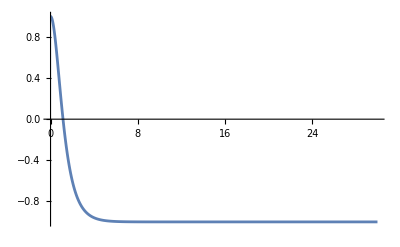

```mathematica
ListPlot[fA[1],Joined->True,PlotRange->All]
```

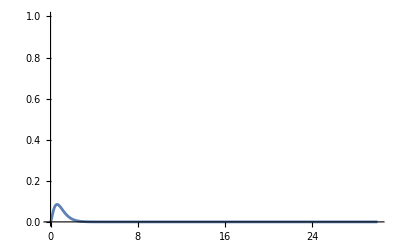

```mathematica
ListPlot[fB[1],Joined->True,PlotRange->{0,1}]
```

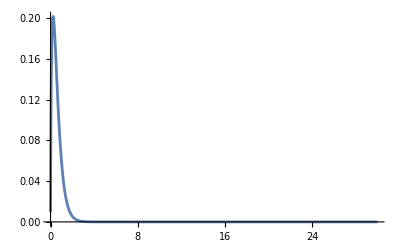

```mathematica
ListPlot[{fC[1]},Joined->True,PlotRange->All]
```

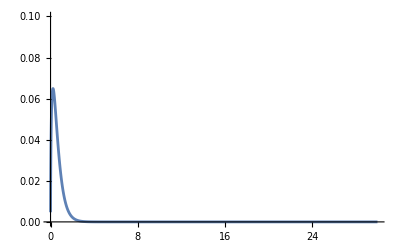

```mathematica
ListPlot[H[1],Joined->True,PlotRange->{0,0.1}]
```

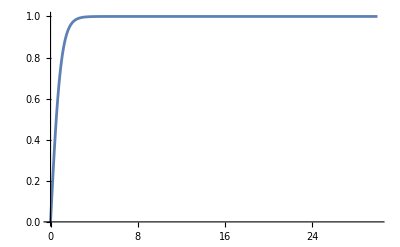

```mathematica
ListPlot[KK[1],Joined->True,PlotRange->All]
```

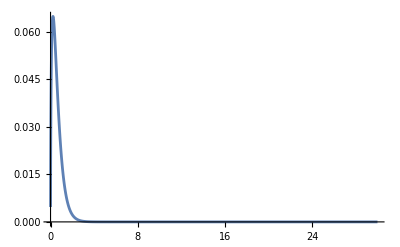

```mathematica
ListPlot[H[1],Joined->True,PlotRange->All]
```

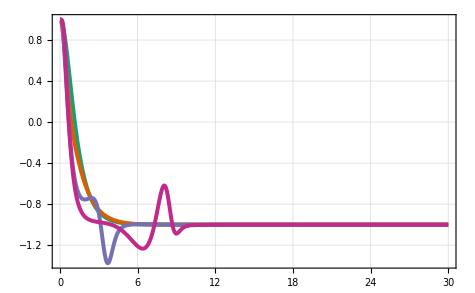

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[fA[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["m_W r",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["f_A(r,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{fA[1],fA[21],fA[51],fA[101]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 2",FontSize->15],MaTeX["t = 5",FontSize->15],MaTeX["t = 10",FontSize->15]},LegendMarkerSize->15],{0.9,0.75}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot   (* <-remove this line if you use Show[…] with fitPlot*)
```

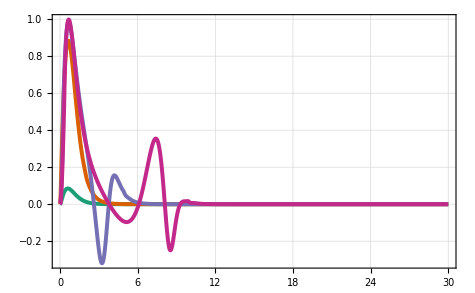

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[fB[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["m_W r",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["f_B(r,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{fB[1],fB[21],fB[51],fB[101]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 2",FontSize->15],MaTeX["t = 5",FontSize->15],MaTeX["t = 10",FontSize->15]},LegendMarkerSize->15],{0.9,0.75}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot   (* <-remove this line if you use Show[…] with fitPlot*)
```

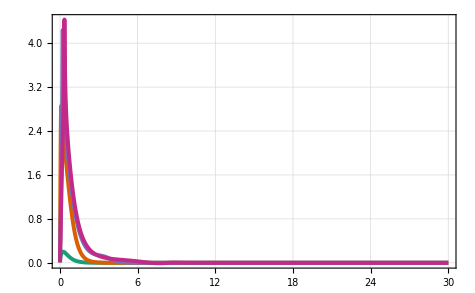

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[fB[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["m_W r",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["f_C(r,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{fC[1],fC[21],fC[51],fC[101]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 2",FontSize->15],MaTeX["t = 5",FontSize->15],MaTeX["t = 10",FontSize->15]},LegendMarkerSize->15],{0.9,0.75}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot   (* <-remove this line if you use Show[…] with fitPlot*)
```

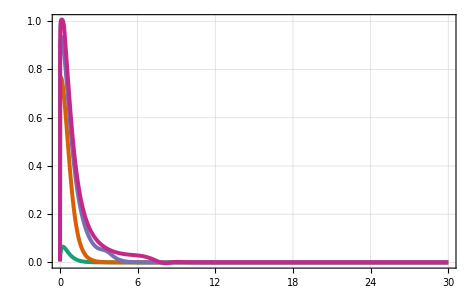

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[H[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["m_W r",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["H(r,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{H[1],H[21],H[51],H[101]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 2",FontSize->15],MaTeX["t = 5",FontSize->15],MaTeX["t = 10",FontSize->15]},LegendMarkerSize->15],{0.9,0.75}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot   (* <-remove this line if you use Show[…] with fitPlot*)
```

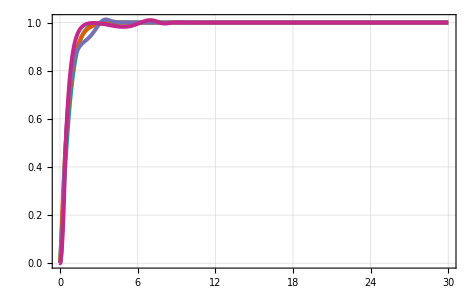

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[KK[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["m_W r",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["K(r,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{KK[1],KK[21],KK[51],KK[101]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 2",FontSize->15],MaTeX["t = 5",FontSize->15],MaTeX["t = 10",FontSize->15]},LegendMarkerSize->15],{0.9,0.55}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
fAint[i_]:=Interpolation[fA[i]];
fBint[i_]:=Interpolation[fB[i]];
fCint[i_]:=Interpolation[fC[i]];
Hint[i_]:=Interpolation[H[i]];
KKint[i_]:=Interpolation[KK[i]];
```

```mathematica
fAGauged[r_,i_]:=Cos[2ArcTan[-(KKint[i][r])/(Hint[i][r])]]fAint[i][r]-Sin[2ArcTan[-(KKint[i][r])/(Hint[i][r])]]fBint[i][r]
fBGauged[r_,i_]:=Sin[2ArcTan[-(KKint[i][r])/(Hint[i][r])]]fAint[i][r]+Cos[2ArcTan[-(KKint[i][r])/(Hint[i][r])]]fBint[i][r]
fCGauged[r_,i_]:=fCint[i][r]-(2 (-(KKint[i][r] Hint[i]'[r])/(Hint[i][r])^2+(KKint[i]'[r])/(Hint[i][r])))/(1+(KKint[i][r])^2/(Hint[i][r])^2)
HGauged[r_,i_]:=Abs[Hint[i][r]*√(1+(KKint[i][r])^2/(Hint[i][r])^2)]
GGauged[r_,i_]:=2(KKint[i][r] Hint[i]'[r]-KKint[i]'[r] Hint[i][r])/((Hint[i][r])^2+(KKint[i][r])^2);
```

```mathematica
timeValues[[100]]
```

9.9

```mathematica
Length[timeValues]
```

501

```mathematica
kVals=Table[k,{k,0.01,10,0.1}];
```

```mathematica
akVals=Association@ParallelTable[k->Table[{timeValues[[t]],(2 k^2)/π Quiet[NIntegrate[(fAGauged[r,t]-1)/r SphericalBesselJ[1,k*r] r^2,{r,0.001,30}]]},{t,1,Length[timeValues],1}],{k,kVals}];
```

```mathematica
bkVals=Association@ParallelTable[k->Table[{timeValues[[t]],(2 k^2)/π Quiet[NIntegrate[1/3((2fBGauged[r,t])/r+fCGauged[r,t]) SphericalBesselJ[0,k*r] r^2,{r,0.001,30}]]},{t,1,Length[timeValues],1}],{k,kVals}];
```

```mathematica
ckVals=Association@ParallelTable[k->Table[{timeValues[[t]],(2 k^2)/π Quiet[NIntegrate[1/3(fBGauged[r,t]/r-fCGauged[r,t]) SphericalBesselJ[2,k*r] r^2,{r,0.001,30}]]},{t,1,Length[timeValues],1}],{k,kVals}];
```

```mathematica
hkVals=Association@ParallelTable[k->Table[{timeValues[[t]],(2 k^2)/π Quiet[NIntegrate[(1-HGauged[r,t]) SphericalBesselJ[0,k*r] r^2,{r,0.001,30}]]},{t,1,Length[timeValues],1}],{k,kVals}];
```

```mathematica
model[t_,A_,k_,ϕ_]:=A Cos[√(k^2+1)t+ϕ]
model2[t_,A_,k_,ϕ_]:=A Cos[√(k^2+1.556^2)t+ϕ]
```

```mathematica
fit=Table[NonlinearModelFit[akVals[kVals[[i]]][[250;;300]],model[t,A,kVals[[i]],ϕ],{{A,1},{ϕ,0}},t],{i,1,Length[kVals]}];
fit2=Table[NonlinearModelFit[Transpose[{bkVals[kVals[[i]]][[150;;200]][[All,1]],bkVals[kVals[[i]]][[150;;200]][[All,2]]-ckVals[kVals[[i]]][[150;;200]][[All,2]]}],model[t,A,kVals[[i]],ϕ],{{A,10},{ϕ,0}},t],{i,1,Length[kVals]}]//Quiet;
fit3=Table[NonlinearModelFit[Transpose[{bkVals[kVals[[i]]][[150;;200]][[All,1]],bkVals[kVals[[i]]][[150;;200]][[All,2]]+2ckVals[kVals[[i]]][[150;;200]][[All,2]]}],model[t,A,kVals[[i]],ϕ],{{A,10},{ϕ,0}},t],{i,1,Length[kVals]}]//Quiet;
fit4=Table[NonlinearModelFit[hkVals[kVals[[i]]][[250;;300]],model2[t,A,kVals[[i]],ϕ],{{A,1},{ϕ,0}},t],{i,1,Length[kVals]}];
```

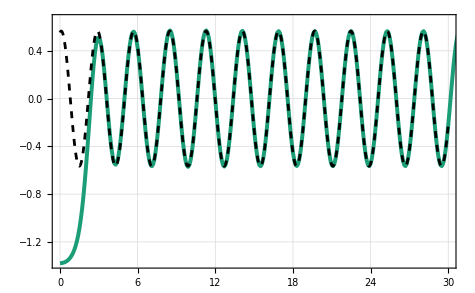

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["t~[m_W^{-1}]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["\\tilde{A}(k,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListPlot[akVals[[21]],Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->{{0,30},All},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)
numPlot2=Plot[model[t,A,kVals[[21]],ϕ]/.fit[[21]]["BestFitParameters"],{t,0,30},PlotStyle->{Black,Dashed}];

Show[numPlot,numPlot2]   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
model[t,A,kVals[[21]],ϕ]/.fit[[21]]["BestFitParameters"]
```

0.565475 Cos[0.209503-2.24502 t]

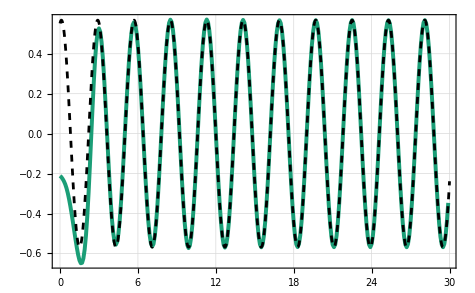

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["t~[m_W^{-1}]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["\\tilde{B}(k,t)-\\tilde{C}(k,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListPlot[Transpose[{bkVals[kVals[[21]]][[1;;300]][[All,1]],bkVals[kVals[[21]]][[1;;300]][[All,2]]-ckVals[kVals[[21]]][[1;;300]][[All,2]]}],Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)
numPlot2=Plot[model[t,A,kVals[[21]],ϕ]/.fit2[[21]]["BestFitParameters"],{t,0,30},PlotStyle->{Black,Dashed}];

Show[numPlot,numPlot2]   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
model[t,A,kVals[[21]],ϕ]/.fit2[[21]]["BestFitParameters"]
```

0.568064 Cos[0.239485-2.24502 t]

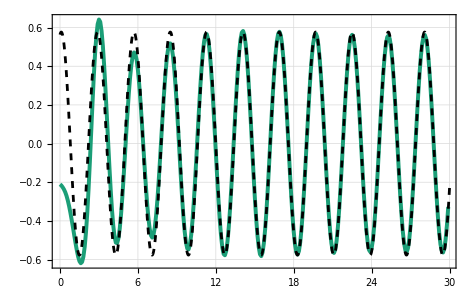

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["t~[m_W^{-1}]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["\\tilde{B}(k,t)+2\\tilde{C}(k,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListPlot[Transpose[{bkVals[kVals[[21]]][[1;;300]][[All,1]],bkVals[kVals[[21]]][[1;;300]][[All,2]]+2ckVals[kVals[[21]]][[1;;300]][[All,2]]}],Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)
numPlot2=Plot[model[t,A,kVals[[21]],ϕ]/.fit3[[21]]["BestFitParameters"],{t,0,30},PlotStyle->{Black,Dashed}];

Show[numPlot,numPlot2]   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
model[t,A,kVals[[21]],ϕ]/.fit3[[21]]["BestFitParameters"]
```

0.576857 Cos[0.215991-2.24502 t]

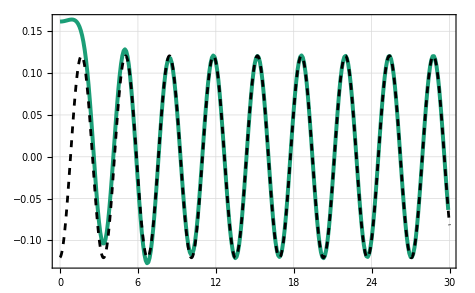

1.01

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["t~[m_W^{-1}]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["\\tilde{H}(k,t)",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListPlot[hkVals[[11]][[1;;300]],Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)
numPlot2=Plot[model2[t,A,kVals[[11]],ϕ]/.fit4[[11]]["BestFitParameters"],{t,0,30},PlotStyle->{Black,Dashed}];

Show[numPlot,numPlot2]   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
model2[t,A,kVals[[11]],ϕ]/.fit4[[11]]["BestFitParameters"]
```

-0.120626 Cos[0.0703711+1.85506 t]

```mathematica
akvsk=Table[{kVals[[i]],Abs[A]/.fit[[i]]["BestFitParameters"]},{i,1,Length[kVals]}];
```

```mathematica
bkvsk=Table[{kVals[[i]],Abs[A]/.fit2[[i]]["BestFitParameters"]},{i,1,Length[kVals]}];
```

```mathematica
ckvsk=Table[{kVals[[i]],Abs[A]/.fit3[[i]]["BestFitParameters"]},{i,1,Length[kVals]}];
```

```mathematica
hkvsk=Table[{kVals[[i]],Abs[A]/.fit4[[i]]["BestFitParameters"]},{i,1,Length[kVals]}];
```

```mathematica
testa=Interpolation[akvsk];
testb=Interpolation[bkvsk];
testc=Interpolation[ckvsk];
testh=Interpolation[hkvsk];
```

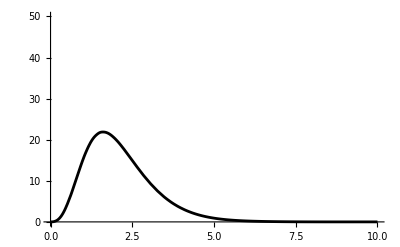

```mathematica
aa=Plot[(2 π^2)/0.653^2((√(1^2+k^2))/k^2(testa[k]^2+testb[k]^2)+1/2 testc[k]^2/(√(1^2+k^2))),{k,0.01,10},PlotRange->{0,50},PlotStyle->Black]
```

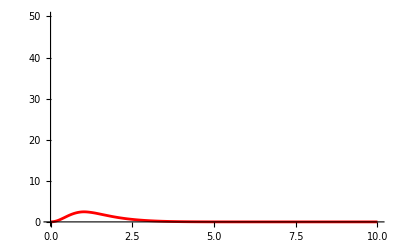

```mathematica
hh=Plot[(2 π^2)/0.653^2(2 √(1.556^2+k^2))/k^2 testh[k]^2,{k,0.01,10},PlotRange->{0,50},PlotStyle->Red]
```

```mathematica
NIntegrate[(2 π^2)/0.653^2((√(1^2+k^2))/k^2(testa[k]^2+testb[k]^2)),{k,0.01,10}]
```

41.5829

```mathematica
NIntegrate[(2 π^2)/0.653^2(1/2 testc[k]^2/(√(1^2+k^2))),{k,0.01,10}]
```

7.76914

```mathematica
NIntegrate[(2 π^2)/0.653^2((√(1^2+k^2))/k^2(testa[k]^2+testb[k]^2)+1/2 testc[k]^2/(√(1^2+k^2))),{k,0.01,10}]
```

49.3521

```mathematica
NIntegrate[(2 π^2)/0.653^2(2 √(1.556^2+k^2))/k^2 testh[k]^2,{k,0.01,10}]
```

4.00328

```mathematica
√0.1
```

0.316228

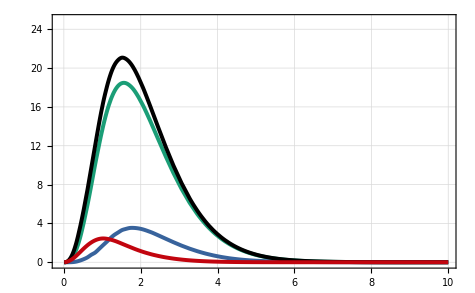

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["k~[m_W]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["dN/dk",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=Plot[{(2 π^2)/0.653^2((√(1^2+k^2))/k^2(testa[k]^2+testb[k]^2)),(2 π^2)/0.653^2(1/2 testc[k]^2/(√(1^2+k^2))),(2 π^2)/0.653^2((√(1^2+k^2))/k^2(testa[k]^2+testb[k]^2+1/2 testc[k]^2/(√(1^2+k^2)))),(2 π^2)/0.653^2(2 √(1.556^2+k^2))/k^2 testh[k]^2},{k,0.01,10},PlotStyle->{{lineSpec[1]},{RGBColor[0.22, 0.39, 0.61],Thickness[0.006]},{RGBColor[0, 0, 0],Thickness[0.006]},{RGBColor[0.76, 0.02, 0.06],Thickness[0.006]}},PlotRange->{{-0.1,10},{-0.1,25}},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{MaTeX["\\rm{Gauge~Bosons~(T)}",FontSize->15],MaTeX["\\rm{Gauge~Bosons~(L)}",FontSize->15],MaTeX["\\rm{Gauge~Bosons}",FontSize->15],MaTeX["\\rm{Higgs~Bosons}",FontSize->15]},LegendMarkerSize->15],{0.82,0.77}                                    (*inside UR corner*)]];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

Show[numPlot]   (* <-remove this line if you use Show[…] with fitPlot*)
```

```mathematica
kin[t_]:=Table[{fAdt[t][[i,1]],(fAdt[t][[i,2]])^2+(fBdt[t][[i,2]])^2+(fAdt[t][[i,1]])^2/2*(fCdt[t][[i,2]])^2+2(fAdt[t][[i,1]])^2*((Hdt[t][[i,2]])^2+(KKdt[t][[i,2]])^2)},{i,Length[fAdt[t]]}]
```

```mathematica
(D[fA[r,t],r]+fC[r,t]*fB[r,t])^2+(D[fB[r,t],r]-fC[r,t]*fA[r,t])^2+((fA[r,t]^2+fB[r,t]^2-1)^2)/(2(r+ϵ)^2)+2 r^2((D[H[r,t],r]+1/2 fC[r,t]*KK[r,t])^2+(D[KK[r,t],r]-1/2 fC[r,t]*H[r,t])^2+1/(2(r+ϵ)^2)(H[r,t]*fA[r,t]+KK[r,t]*fB[r,t]-H[r,t])^2+1/(2(r+ϵ)^2)(KK[r,t]*fA[r,t]-H[r,t]*fB[r,t]+KK[r,t])^2)+1/2 r^2(H[r,t]^2+KK[r,t]^2-1)^2;
```

-Graphics-

```mathematica
pot[t_]:=Table[{fAdt[t][[i,1]],(fAdr[t][[i,2]]+fC[t][[i,2]]*fB[t][[i,2]])^2+(fBdr[t][[i,2]]-fC[t][[i,2]]*fA[t][[i,2]])^2+(((fA[t][[i,2]])^2+(fB[t][[i,2]])^2-1)^2)/(2(fAdt[t][[i,1]])^2)+2(fAdt[t][[i,1]])^2((Hdr[t][[i,2]]+1/2 fC[t][[i,2]]*KK[t][[i,2]])^2+(KKdr[t][[i,2]]-1/2 fC[t][[i,2]]*H[t][[i,2]])^2+1/(2(fAdt[t][[i,1]])^2)(H[t][[i,2]]*fA[t][[i,2]]+KK[t][[i,2]]*fB[t][[i,2]]-H[t][[i,2]])^2+1/(2(fAdt[t][[i,1]])^2)(KK[t][[i,2]]*fA[t][[i,2]]-H[t][[i,2]]*fB[t][[i,2]]+KK[t][[i,2]])^2)+1/2(fAdt[t][[i,1]])^2((H[t][[i,2]])^2+(KK[t][[i,2]])^2-1)^2},{i,Length[fAdt[t]]}]
```

```mathematica
full[t_]:=Table[{fAdt[t][[i,1]],29.47890374441791((fAdt[t][[i,2]])^2+(fBdt[t][[i,2]])^2+(fAdt[t][[i,1]])^2/2*(fCdt[t][[i,2]])^2+2(fAdt[t][[i,1]])^2*((Hdt[t][[i,2]])^2+(KKdt[t][[i,2]])^2)+(fAdr[t][[i,2]]+fC[t][[i,2]]*fB[t][[i,2]])^2+(fBdr[t][[i,2]]-fC[t][[i,2]]*fA[t][[i,2]])^2+(((fA[t][[i,2]])^2+(fB[t][[i,2]])^2-1)^2)/(2(fAdt[t][[i,1]])^2)+2(fAdt[t][[i,1]])^2((Hdr[t][[i,2]]+1/2 fC[t][[i,2]]*KK[t][[i,2]])^2+(KKdr[t][[i,2]]-1/2 fC[t][[i,2]]*H[t][[i,2]])^2+1/(2(fAdt[t][[i,1]])^2)(H[t][[i,2]]*fA[t][[i,2]]+KK[t][[i,2]]*fB[t][[i,2]]-H[t][[i,2]])^2+1/(2(fAdt[t][[i,1]])^2)(KK[t][[i,2]]*fA[t][[i,2]]-H[t][[i,2]]*fB[t][[i,2]]+KK[t][[i,2]])^2)+1/2(fAdt[t][[i,1]])^2((H[t][[i,2]])^2+(KK[t][[i,2]])^2-1)^2)},{i,Length[fAdt[t]]}]
```

```mathematica
timeValues[[51]]
```

5.

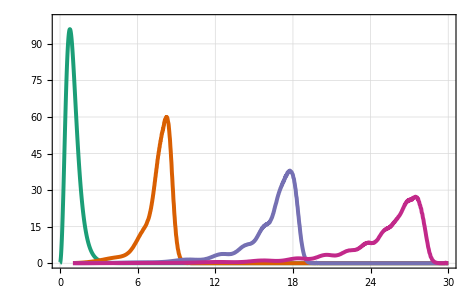

```mathematica
Needs["MaTeX`"];
ffont="CMU Classical Serif";
nfont="CMU Serif";
(*----------------------------------------------------------------------*)(*1. Settings*)(*----------------------------------------------------------------------*)times={1,11,21,31};                     (*snapshots you want*)
niceColors={RGBColor["#1b9e77"],(*dark teal*)RGBColor["#d95f02"],(*orange‑brown*)RGBColor["#7570b3"],(*muted purple*)RGBColor["#c2298a"],(*magenta*)RGBColor["#6961e"]    (*olive green*)};

lineSpec[i_]:={niceColors[[i]],Thickness[0.006]};
dashSpec[i_]:={niceColors[[i]],Dashed,Thick,Opacity[0.8]}; (*for fits*)

(*----------------------------------------------------------------------*)
(*2. Prepare data*)
(*----------------------------------------------------------------------*)
profiles=Table[fA[t],(*numeric profile*){t,times}];

(*If you also have analytic/spline fits,uncomment and fill these lines*)
(*fitProfiles=Table[fAFit[t],{t,times}];*)
xLabel=MaTeX["t~[m_W^{-1}]",FontSize->18];          (*16‑pt Canvas‑embedded PDF*)
yLabel=MaTeX["dE(r)/dr~[m_W]",FontSize->18];

(*----------------------------------------------------------------------*)
(*3. Plot*)
(*----------------------------------------------------------------------*)
numPlot=ListLinePlot[{full[1],{-10,-10},{-10,-10},{-10,-10}},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->{{0,30},{0,100}},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotLegends->Placed[LineLegend[{MaTeX["t = 0",FontSize->15],MaTeX["t = 10",FontSize->15],MaTeX["t = 20",FontSize->15],MaTeX["t = 30",FontSize->15]},LegendMarkerSize->15],{0.9,0.76}                                    (*inside UR corner*)],PlotTheme->"Scientific"];

(*If you have fits,overlay them as dashed versions in the same colors*)
(*fitPlot=ListLinePlot[fitProfiles,Joined->True,PlotStyle->Table[dashSpec[i],{i,Length[times]}],PlotRange->All];
Show[numPlot,fitPlot]*)

numPlot2=ListLinePlot[{{-10,-10},Select[full[101],#[[1]]>1&],Select[full[201],#[[1]]>1&],Select[full[301],#[[1]]>1&]},Joined->True,PlotStyle->Table[lineSpec[i],{i,Length[times]}],PlotRange->{{0,30},{0,100}},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{xLabel,yLabel},LabelStyle->14,ImageSize->475,GridLines->Automatic,PlotTheme->"Scientific"];

Show[numPlot,numPlot2]   (* <-remove this line if you use Show[…] with fitPlot*)
```